# Universal Estimator

## Parameter range adjustment

For convenience, we want to work with parameters  ∈ (0,1) and map them to the parameters in the original range.
For that, we can use the Logistic function and its Logit inverse.

#### The Logistic function

The standard Logistic function, σ(x), defined in (-∞, ∞) and yields values in (0,1):

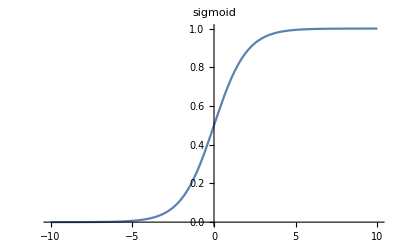

```mathematica
Sigmoid[x_]:=1/(1+ⅇ^-x)
Plot[Sigmoid[x], {x, -10, +10}, PlotLabel->HoldForm[sigmoid]]
```

#### The Logit function

The Logit  is the inverse of the Logistic function σ(x), defined in (0,1) and yields values in (-∞, ∞).
Let’s find the inverse:
σ(x) = y =  1/(1+e^-x) ⇒  1+e^-x = 1/y  ⇒  e^-x = 1/y-1=(1-y)/y  ⇒  log(e^-x)=log((1-y)/y)  ⇒  -x = log((1-y)/y)  ⇒  x = log(y/(1-y)) = σ^-1(x)

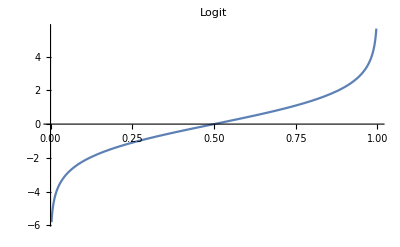

```mathematica
Logit[x_]:= Log[x/(1-x)]
Plot[Logit[x], {x, 0, 1}, PlotLabel->HoldForm[Logit]]
```

### Range Adjuster

We define an Adjuster function which returns another function that maps a parameter in the range  (0,1) to the range  (low, high) of the original distribution.
We can use the Logistic function and its Logit inverse as follows:
Let
	h(t) = Logit(t) , t ∈ (0,1)
Than
	h^-1(d) = Sigmoid(d) , d ∈ (-∞, ∞)

```mathematica
Adjuster[low_, high_]:=With[{LOW=Sigmoid[low],HIGH=Sigmoid[high]}, Function[{t},Logit[LOW+t(HIGH-LOW)]]]
```

### Test Adjuster

For example, we can create an Adjuster for the range [2,5] and call it with values ∈ [0,1]

```mathematica
adj=Adjuster[2, 5];
Print[adj[0.01]];
```

2.01076

```mathematica
Print[adj[0.99]];
```

4.84348

Plot of the adjuster output in the range [0,1]

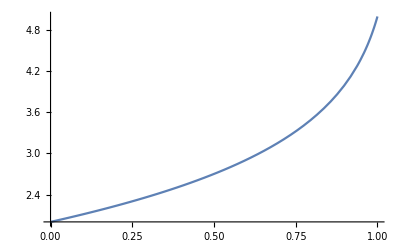

```mathematica
Print[Plot[adj[x], {x,0,1}]]
```

## Generate data

Arguments:

nSamples: number of samples to generate

M: number of observations in each sample

f: the function to generate samples

ranges: an array [d X 2] of parameter ranges (e.g. for 2 parameters: [[0, 10], [0, ∞]])

bins: number of bins in histograms (default: max[samples]+1)

Returns:

a table of associations: histogram -> params (over all samples)

```mathematica
GenerateData[nSamples_, M_, f_, ranges_, bins_:-1]:= 
Module[{nParams, adjusters, params,samples, nbins},

(*number of parameters*)
nParams=Dimensions[ranges][[1]];

(*generate an adapter for each parameter range*)
adjusters=Table[Adjuster[ranges[[i,1]],ranges[[i,2]]],{i,1,nParams}];

(*generate N parameters cube in the range (0,1)*)
params=Table[adjusters[[j]][RandomReal[{0,1}]],{i,1,nSamples},{j,1,nParams}];

(*output*)
(*generate N samples from the parameters*)
samples=Table[f[params[[i]],M],{i,1,nSamples}];

(*create a histogram from each sample*)
nbins=If [bins>0,bins,Max[samples]+1];
h[x_]:=HistogramList[x, {0,nbins,1}][[2]];

(*output*)
Table[h@samples[[i]]-> params[[i]], {i, 1, nSamples}]
]
```

Test GenerateData

```mathematica
YuleSimon[{α_,β_}, M_]:=RandomVariate[WaringYuleDistribution[α,β],M];
YuleSimonRanges = {{2,3},{0,10}};

Print[];
Print["YuleSimon"];
YuleSimonData = GenerateData[5,10,YuleSimon, YuleSimonRanges];
Print[YuleSimonData//TableForm];
```

YuleSimon

{9,1,0,0,0,0,0,0}→{2.02376,0.206439}
{8,0,1,1,0,0,0,0}→{2.7548,1.7716}
{8,0,1,1,0,0,0,0}→{2.04269,2.59007}
{8,2,0,0,0,0,0,0}→{2.97036,1.37718}
{6,0,2,1,0,0,0,1}→{2.62729,2.20344}

## DNN

NetGraph[<>]

{2.1,0.5}

Evaluate params:{2.1,0.5}

Predicted:{2.45105,0.568545}

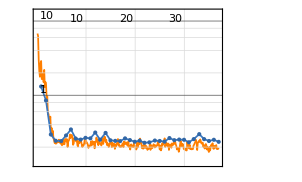
NetTrainResultsObject[NetTrain Results
summary | ,,  batches:592  rounds:37  time:18s  examples/s:2124
data | ,,  training examples:1000  validation examples:250  processed examples:37888  skipped examples:0
method | ,,  ADAMoptimizer  batch size64CPU
round | ,,  loss:1.97×10^-1
validation | ,,  loss:2.36×10^-1
 | rounds
loss | -Graphics- | 
-Graphics-  training set	-Graphics-  validation set | ]

```mathematica
CreateNet[bins_, nParams_]:=( 
NetChain[{
LinearLayer[bins], 
(*BatchNormalizationLayer[],*)
ElementwiseLayer[Ramp], 
(*DropoutLayer[0.2],*)
LinearLayer[bins], 
(*BatchNormalizationLayer[],*)
ElementwiseLayer[Ramp], 
(*DropoutLayer[0.2],*)
LinearLayer[bins], 
(*BatchNormalizationLayer[],*)
ElementwiseLayer[Ramp], 
(*DropoutLayer[0.2],*)
LinearLayer[bins], 
(*BatchNormalizationLayer[],*)
ElementwiseLayer[Ramp], 
(*DropoutLayer[0.2],*)
LinearLayer[nParams]},
"Input"->bins, 
"Output" -> nParams]
)

(*test DNN*)
M = 256;
nSamples = 1000;

(*generate data*)
trainSet=GenerateData[nSamples,M,YuleSimon, YuleSimonRanges];
bins = Length@trainSet[[1]][[1]];
valSet=GenerateData[nSamples/4,M,YuleSimon, YuleSimonRanges, bins];

(*train*)
nParams=Dimensions[YuleSimonRanges][[1]];
net = NetInitialize@CreateNet[bins, nParams];
Print[NetGraph[net]];
results=NetTrain[net,
trainSet,
All, Method->"ADAM", 
ValidationSet->valSet, 
LossFunction->MeanAbsoluteLossLayer[]];

(*evaluate*)
params={2.1,0.5}
Print["Evaluate params:", params];
trained = results["TrainedNet"];
predicted = trained[HistogramList[YuleSimon[params,M],{0,bins,1}][[2]]];
Print["Predicted:", predicted];

(*Plot NetTrain Results*)
Print[results];
```

## Experiments

Define some longtail distributions.
Run an experiment for each longtail distribution.

Assuming 2 parameters for the distribution:

Generate learning samples (train/val) for the given parameters ranges (using GenerateData defined above).

Train a NN model for predicting the parameters corresponding to each sample.

Create a 2-dimensional parameters mesh on the unit square, with 0.1 resolution (i.e: 0.1, 0.2, ... , 0.9)
The mesh is a cube of size 9^2 (81 cell matrix), each containing pair of parameter values (t_1,t_2) ∈ [0.1,...,0.9]

At each mesh point:

Run several trials. At each trial:

Create test data (a histogram of a sample generated at that mesh point)

Predict the parameters at the mesh point, averaging the prediction error.

Compute the Cramer-Raw bound for the mesh point.

Record the relation  (prediction error)/(Cramer-Raw bound)

Plot a surface of the relation above at each mesh point, hopefully showing a value around 2 at each point.

#### Define longtail distributions

```mathematica
(*Sample M observations from the Yule distribution with shape parameters α and β.*)
YuleSimonRV[{α_,β_}, M_]:=RandomVariate[WaringYuleDistribution[α,β],M];

(*Sample M observations from the PowerLaw distribution with domain parameter k and shape parameter a.*)
PowerLawRV[{k_,a_}, M_]:=RandomVariate[PowerDistribution[k,a],M];

(*Log-Normal*)
LogNormalRV[{μ_,σ_}, M_]:=RandomVariate[LogNormalDistribution[μ,σ],M];
```

#### Define an Association for each distribution

```mathematica
distributions = Association[
"yulesimon" -> Association["dist"->YuleSimonRV, "ranges"->{{2,3},{0,10}}, "M"->256],
"powerlaw" -> Association["dist"->PowerLawRV, "ranges"->{{1,10},{0,10}}, "M"->256],
"lognormal" -> Association["dist"->LogNormalRV, "ranges"->{{1,3},{0,5}}, "M"->256]
];
```

```mathematica
(*test association*)
dist = distributions["yulesimon"];
f = dist["dist"];
ranges = dist["ranges"];
M = dist["M"];
f[ranges[[1]], M]
```

{3,9,7,2,0,0,8,0,0,0,1,2,3,0,1,1,0,0,1,0,0,0,0,1,1,0,0,2,3,2,2,0,1,0,0,2,2,9,4,1,1,0,2,7,1,0,12,0,3,7,0,17,0,0,7,0,2,0,6,10,4,5,0,0,0,1,1,3,0,11,0,0,10,2,2,0,0,0,0,3,5,0,1,6,0,2,0,0,1,6,3,0,0,3,2,27,0,0,1,0,0,0,0,29,0,3,1,15,19,12,1,1,7,2,3,0,0,1,1,0,9,4,3,0,4,18,0,1,4,3,0,2,0,1,0,0,1,8,1,1,0,3,0,3,0,0,0,0,1,4,0,0,5,7,0,0,0,0,1,0,0,0,1,1,0,0,0,1,1,0,1,0,7,0,8,1,2,9,4,3,1,0,1,1,1,5,6,3,1,0,0,0,1,4,0,1,0,2,0,0,0,2,0,0,1,4,0,9,5,0,1,0,0,2,0,5,0,31,1,0,6,1,2,5,1,1,1,0,0,0,0,0,3,12,8,1,10,0,1,2,0,0,7,2,0,0,5,4,0,10,3,2,2,5,1,0}

### Run the experiments

An experiment for a single distribution

```mathematica
RunExperiment[distributions_, distname_]:=
Module[{dist, f, ranges, M, nSamples, trainSet, bins, valSet, nParams, net, model, adjuster1, adjuster2, mesh},
(*Get definitions for the distribution specified by distname*)
dist = distributions[distname];
f = dist["dist"];
ranges = dist["ranges"];
M = dist["M"];

(*Train the network*)
{model, bins} = TrainNet[f, ranges, M];

(*Evaluate*)
EvaluateModel[model, ranges, M, bins]
]

TrainNet[f_, ranges_, M_]:=Module[{dist, nSamples, trainSet, bins, valSet, nParams, net, model},
(*Generate learning samples (train/val) for the parameters ranges (using GenerateData defined above).*)
nSamples = 1000;
trainSet=GenerateData[nSamples,M,f, ranges];
(*we need the same number of bins for the validation set*)
bins = Length@trainSet[[1]][[1]];
valSet=GenerateData[nSamples/4,M,f, ranges, bins];

(*Train a NN model for predicting the parameters corresponding to each sample.*)
nParams=Dimensions[ranges][[1]];
net = NetInitialize@CreateNet[bins, nParams];
model=NetTrain[
net,trainSet,
All,
Method->"ADAM", 
ValidationSet->valSet, 
LossFunction->MeanAbsoluteLossLayer[]];

(*output model & input size*)
{model, bins}
]

EvaluateModel[model_, ranges_, M_, bins_]:=Module[{adjuster1, adjuster2, mesh},

(*Create an adjuster for each parameter*)
adjuster1=Adjuster[ranges[[1,1]],ranges[[1,2]]];
adjuster2=Adjuster[ranges[[2,1]],ranges[[2,2]]];

(*Create a 2-dimensional parameters mesh on the unit square*)
mesh = Table[{adjuster1[i],adjuster2[j]},{i,0.1,0.9,0.1 },{j,0.1,0.9,0.1 }];

(*output*)
(*Process each mesh point*)
Table[EvaluateMeshPoint[model, f, mesh[[i,j]], M, bins],{i,1,9 },{j,1,9 }]
]

EvaluateMeshPoint[model_, f_, params_, M_, bins_]:= 
Module[{sample, histogram, cycles, predicted, error},
(*Run n cycles*)
error=0;
cycles=3;
For[i=0; , i < cycles, i+=1,
(*Create a histogram from a sample generated using the given parameters)*)
sample=f[params,M];
histogram = HistogramList[sample, {0,bins,1}][[2]];

(*Predict the parameters, averaging the prediction absolute error.*)
predicted = model[histogram];
error += Abs[predicted - params];
];

(*avg the errors across all parameters*)
error=Mean[error /cycles];

(*Compute the Cramer-Raw bound for the mesh point.*)
(*Return the relation(prediction error)/(Cramer-Raw bound)*)
error/CramerRawBound[params, M]
]

CramerRawBound[params_, M_]:=Module[{},
(*lilo:TODO*)
0.2
]
```

```mathematica
(*RunExperiment[distributions, "yulesimon"]*)
dist = distributions["yulesimon"];
f = dist["dist"];
ranges = dist["ranges"];
M = dist["M"];
{model, bins} = TrainNet[f, ranges, M];
```

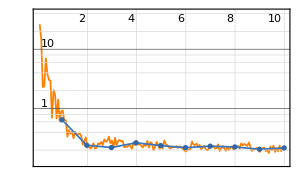
NetTrainResultsObject[NetTrain Results
summary | ,,  batches:160  rounds:10  time:29s  examples/s:361
data | ,,  training examples:1000  validation examples:250  processed examples:10240  skipped examples:0
method | ,,  ADAMoptimizer  batch size64CPU
round | ,,  loss:2.07×10^-1
validation | ,,  loss:2.18×10^-1
 | rounds
loss | -Graphics- | 
-Graphics-  training set	-Graphics-  validation set | ]

```mathematica
model
```

```mathematica
trained = model["TrainedNet"];
EvaluateModel[trained, ranges, M, bins]
```

{{1.01751,0.678637,1.10084,0.995105,0.899564,0.87381,0.573854,0.979564,0.820104},{0.917503,0.799331,0.797675,0.827523,0.845644,1.11881,0.995187,0.548198,1.53699},{0.624522,0.781887,1.0555,1.52216,0.742838,0.889749,0.8477,0.310671,0.631189},{0.444289,0.824962,0.879709,0.712636,0.989829,0.893302,0.606138,0.933559,0.764022},{0.195392,0.743883,0.87752,0.613595,1.12816,0.375823,0.807487,0.87664,0.990043},{0.245013,0.698137,0.801554,0.94421,0.986882,0.746326,1.14036,0.859856,0.603366},{0.530284,0.63322,0.952072,1.06518,0.871129,0.844052,0.661783,0.48989,0.613466},{0.821819,0.6623,1.17008,0.956591,0.756177,0.571172,0.779047,0.692924,0.732694},{1.03619,0.492468,1.10895,1.1403,0.648292,1.20506,0.950378,0.556559,0.520987}}

Fisher Information

```mathematica
(*single parameter*)
FI[dist_]:= (
f=PDF[dist[α],x]; 
h=D[Log[f],{α,2}];
(fim=Expectation[-h,x\[Distributed]dist[α]])
)

(*two parameters*)
FIM[dist_]:= (
f=PDF[dist[α,β],x]; 
h=D[Log[f],{{α,β},2}];
(fim=Expectation[-h,x\[Distributed]dist[α,β]])//MatrixForm
)
```

### Examples

```mathematica
FIM@NormalDistribution
```

(1/β^2 | 0
0 | 2/β^2)

```mathematica
FIM@PowerDistribution
```

(β/α^2 | -1/α
-1/α | 1/β^2)

```mathematica
FIM@LogNormalDistribution
```

(1/β^2 | 0
0 | 2/β^2)

```mathematica
FI@PoissonDistribution
```

1/α